Analytically solves the 2D system at zero k and zero l as a function of the shear rate γd at a given value of activity. Investigates the relationship between the real and imaginary parts of the solutions and the shapes of the stability phase boundaries.

```mathematica
sigmasoln = Solve[(τ a)/η==((1+σ τ)^2/(γd τ)+γd τ)/((λ(1+σ τ))/(γd τ(1+γd^2 τ^2))-(γd λ τ)/(1 + γd^2 τ^2)),σ]/.{τ->1,η->1,λ->1}//FullSimplify
```

{{σ→-(2-a+2 γd^2+√(a^2-4 (γd+γd^3)^2-4 a (γd^2+γd^4)))/(2 (1+γd^2))},{σ→(-2+a-2 γd^2+√(a^2-4 (γd+γd^3)^2-4 a (γd^2+γd^4)))/(2 (1+γd^2))}}

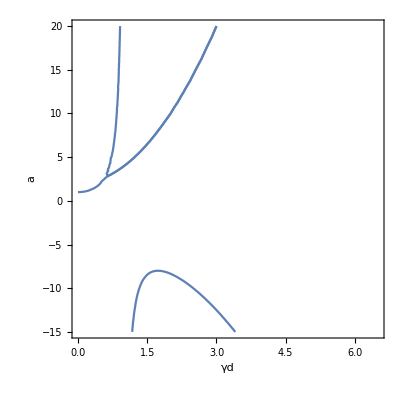

```mathematica
p1=ContourPlot[Re[σ/.sigmasoln[[1]]]==0,{γd,0,6.5}, {a,-15,20},AxesLabel->{"γd","a"}];
p2=ContourPlot[Re[σ/.sigmasoln[[2]]]==0,{γd,0,6.5}, {a,-15,20},AxesLabel->{"γd","a"}];
Show[p1,p2]
```

```mathematica
Show[p1,p2]
```

The following results show that, there is some value of γd at which the imaginary parts of both σ_1 and σ_2 become non-zero. Moreover, since the only source of imaginary components in them can only have come from the expression under the square root, the real parts of the two branches merge together, while the imaginary parts diverge (see below).

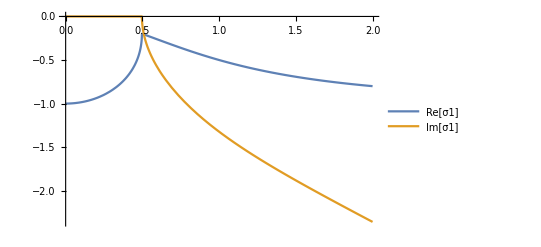

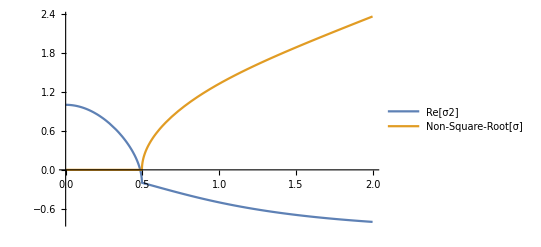

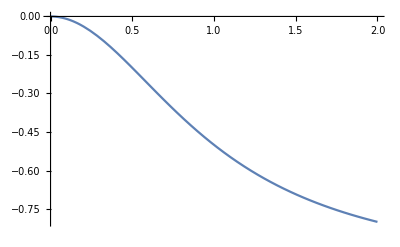

```mathematica
aval = 2;
NonSqrtPart[γd_]=-(2-a+2 γd^2)/(2 (1+γd^2));
SqrtPart[γd_]=a^2-4 (γd+γd^3)^2-4 a (γd^2+γd^4);
(*NSolve[SqrtPart[γd]==0/.a->aval];*)
Plot[ {Re[σ/.sigmasoln[[1]]]/.a->aval,Im[σ/.sigmasoln[[1]]]/.a->aval},{γd,0,2},PlotLegends->{"Re[σ1]","Im[σ1]"}]
Plot[ {Re[σ/.sigmasoln[[2]]]/.a->aval,Im[σ/.sigmasoln[[2]]]/.a->aval},{γd,0,2},PlotLegends->{"Re[σ2]","Non-Square-Root[σ]","Im[σ2]"}]
Plot[NonSqrtPart[γd]/.a->aval, {γd,0,2}]
```

The below shows that the two-fork shape of the stability phase boundary is a result of the fact that beyond a certain activity value, the real part of σ starts to have two zeros, and therefore two possible places where the system can go from stability to instability.

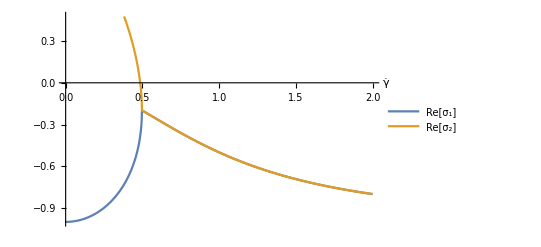

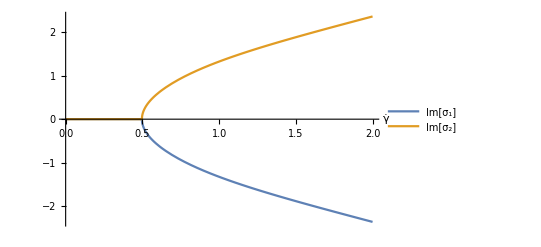

```mathematica
Plot[ {Re[σ/.sigmasoln[[1]]]/.a->aval,Re[σ/.sigmasoln[[2]]]/.a->aval},{γd,0,2},PlotLegends->{"Re[σ_1]","Re[σ_2]"},AxesLabel->{OverDot[γ]}]
Plot[ {Im[σ/.sigmasoln[[1]]]/.a->aval,Im[σ/.sigmasoln[[2]]]/.a->aval},{γd,0,2},PlotLegends->{"Im[σ_1]","Im[σ_2]"},AxesLabel->{OverDot[γ]}]
```

```mathematica
asoln = Solve[(τ a)/η==((1+σ τ)^2/(γd τ)+γd τ)/((λ(1+σ τ))/(γd τ(1+γd^2 τ^2))-(γd λ τ)/(1 + γd^2 τ^2)),a]/.σ->0//FullSimplify
```

{{a→-(η (1+γd^2 τ^2)^2)/(λ τ (-1+γd^2 τ^2))}}